## μQuans Conversion

-Graphics-

#### Freq (atom)

All units in MHz.
μQ master laser is locked on Rb85 3->3x4 (fmaster).
Cooling light: Rb87 2->3 (fS0res)

```mathematica
f85master=384230406.373-1264.889+120.64/2-20.435;
f87cooling=384230484.4685 - 2563.006+193.7408;
f87rep=f87cooling-266.65+6834.68;
ΔfRepCool=f87rep-f87cooling;
```

Frequency difference between these is around 1GHz.

```mathematica
f85master-f87cooling
```

1066.17

```mathematica
f87rep-f87cooling
```

6568.03

#### The laser

the lasers are running at telecom λ. S0 laser also has a 110 MHz AOM before doubling before the output. So they must have introduced a offset of 110 MHz in the beating.
We need to half the frequency. 
This means: the beat note frequency for resonance light is 643 MHz.
All these are theoretical!!!!

```mathematica
Δflaser[δ_]:=f85master/2-(f87cooling/2-110+δ/2);(*@ 1550*)
Δflaser[δ_,fAOM_]:=f85master/2-(f87cooling/2-110+δ/2-fAOM/2);(*@ 1550*)
```

The lasers are telecom we need to half the frequency.

```mathematica
Δflaser[0]
```

643.083

test: 
according the μQans, at -15 MHz S0 red tetuned from 2->3 resonance should give 650MHz.... perfect.

```mathematica
Δflaser[-15]
```

650.583

Lets now see what happens when fibre(135MHz) AOMs are included (carrier freq.:133.5 MHz)

#### DDS freq

now let us introduce DDS frequency.
For S0, f_1560= 8 f_DDS 
f85master-(8 ddsS0)2: freq of S0laser in 780nm
... +2 110+fAOM : Going through AOM and fibre AOM

```mathematica
getS0DDS[δ_,fAOM_]:=ddsS0/.First[Solve[f85master-(8 ddsS0)2+2 110+fAOM-(f87cooling+δ)==0,ddsS0]]
```

```mathematica
getS0DDS[-0,133.5]
```

88.7291

```mathematica
getMPhiDDS[δ_,fAOM_]:=ddsMPhi/.First[Solve[
f85master-(8 getS0DDS[δ,fAOM])2 +(3500-2 ddsMPhi)2 +2 110+fAOM -f87rep==0,ddsMPhi]]
```

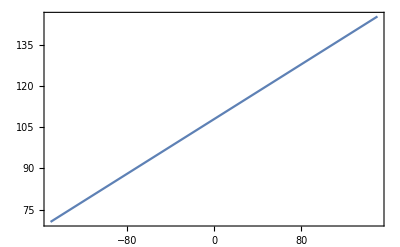

```mathematica
Plot[getMPhiDDS[δ,133.5],{δ,-150,150}]
```

#### Repump freq

Since repump is a sideband of s0 laser.
ideally the repump need to be at

```mathematica
ΔfRepCool
```

6568.03

```mathematica
fRep[δ_,ddsRep_]:=f85master-2Δflaser[δ]+2 110+(3500-2 ddsRep)2 (*@ 780nm*)
fRepWithFibreAOM[δ_,fAOM_,ddsRep_]:=f85master-2ΔflaserWithFibreAOM[δ,fAOM]+2 110+(3500-2 ddsRep)2+fAOM
```

```mathematica
fRep[-15,104.25]-f87cooling
```

6568.

```mathematica
fRepWithFibreAOM[-15,133.5,104.25]-f87cooling
```

8002.67-2 ΔflaserWithFibreAOM[-15,133.5]

```mathematica
mphidds[δ_,fAOM_]:=ddsRep/.Solve[fRepWithFibreAOM[δ,fAOM,ddsRep]-f87rep==0,ddsRep]//First
```

```mathematica
mphidds[-150,133.5]
```

-0.25 (-1851.64+2. ΔflaserWithFibreAOM[-150,133.5])

#### Summary

```mathematica
getDDS[δ_,fAOM_]:={getS0DDS[δ,fAOM],getMPhiDDS[δ,fAOM]}
```

```mathematica
getDDS[-6,133.5]
```

{89.1041,106.492}

```mathematica
{88.72910624742508,107.9924999922514}
```

{88.7291,107.992}

On resonance:
107 DDS mphi gives 266MHz detuning

we want a total detuning of 362.425 MHz between the cooling and the repump, in order to keep Cooling between F’=2 and F’=3 and repump on resonance with F=0.

To get correct mPHI-DDS freq, this situation corresponds to a cooling light at +95.775MHz, leading to a mphi freq of
mϕDDS = 131.936
S0dds = 97.619 at 266.65/2 red detuned.

we have to 

This should corresponds to cooling light at + 229

```mathematica
getS0DDS[-2,133.5]
getMPhiDDS[-3,133.5]
```

88.8541

107.242

```mathematica
Solve[getS0DDS[x,133.5]==129,x]
```

{{x→-644.334}}

```mathematica
(266.65+156.9+72.2)
```

495.75

```mathematica
%-266.65
```

229.1

```mathematica
fcooling=Transpose[{Range[10,-150,-1],getDDS[#,133.5]⟦1⟧&/@Range[10,-150,-1]}];
frep=Transpose[{Range[10,-150,-1],getDDS[#,133.5]⟦2⟧&/@Range[10,-150,-1]}];
```

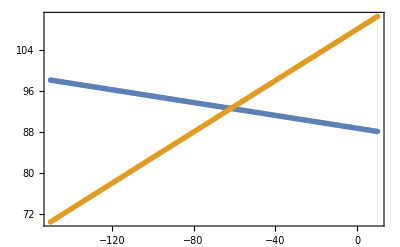

```mathematica
ListPlot[{fcooling,frep}]
```

```mathematica
LinearModelFit[fcooling,x,x]
LinearModelFit[frep,x,x]
```

FittedModel[88.7291-0.0625 x]

FittedModel[107.992+0.25 x]

```mathematica
1/(25 10^6)
```

1/25000000

```mathematica
1.0 %
```

4.×10^-8